```mathematica
Get[NotebookDirectory[]<>#]&/@
{
"combine_packages.wls",
"load_takahashi_data.wl",
"load_Ducret_data.wl"
};
```

```mathematica
figureNumberSteadyState1DShort="Fig_3";
figureNumberSteadyState1DLong=figureNumberSteadyState1DShort<>"_steady_states";
```

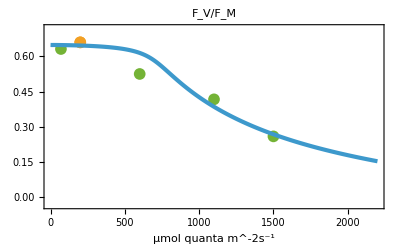

```mathematica
(*Fv/Fm versus light*)
(Export[NotebookDirectory[]<>figureNumberSteadyState1DLong<>"/"<>figureNumberSteadyState1DShort<>"_light_top_left"<>".pdf",#];#)&@Show[
ListPlot[{dataDucretFig3BControlMean,{Join[{200},Normal@data["FigS1"][Select[#["h"]==0.5∧#["temp"]==25.&]][All,"Fv/Fm"]]}},
imageSizePadding[ImagePaddingXunits],PlotMarkers->plotMarkers,PlotRange->{{Lrange[[1]],Lrange[[2]]},{FvFmMinPlot,FvFmMaxPlot}},PlotStyle->{{Dashed,colorPoints2,thickness},{Dashed,colorPoints,thickness}},Joined->False,style],
makeOneSimulationSteadyStatePlot[pars[-6],L,Lrange,FvFm,24 3600,{PlotStyle->{{colorCurves,thickness}},PlotRange->{{Lrange[[1]],Lrange[[2]]},{FvFmMinPlot,FvFmMaxPlot}}}],
PlotRange->{All,{FvFmMinPlot, FvFmMaxPlot}},FrameLabel->{{None,None},{L/.units,None}},PlotLabel->"F_V/F_M"]
```

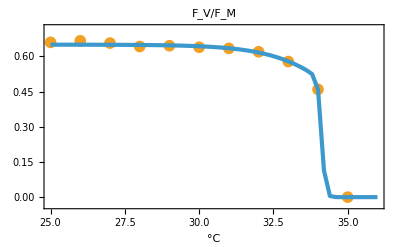

```mathematica
(*Fv/Fm versus temperature*)
(Export[NotebookDirectory[]<>figureNumberSteadyState1DLong<>"/"<>figureNumberSteadyState1DShort<>"_temperature_top_right"<>".pdf",#];#)&@Show[
ListPlot[Normal[data["FigS1"][Select[#["h"]==0.5&]][All,{#["temp"],#["Fv/Fm"]}&]],
imageSizePadding[ImagePaddingXunits],PlotMarkers->plotMarkers,AxesOrigin->{Automatic},PlotStyle->{{Dashed,colorPoints,thickness}},Joined->False,style,
PlotRange->{{wRange1D[[1]],wRange1D[[-1]]},{FvFmMinPlot,FvFmMaxPlot}}
],
makeOneSimulationSteadyStatePlot[Join[{L->0},pars[-6]],w,wRange1D,FvFm,24 3600,{PlotStyle->{{colorCurves,thickness}}}]
,PlotRange->{{wRange1D[[1]],wRange1D[[-1]]},{FvFmMinPlot,FvFmMaxPlot}},FrameLabel->{{None,None},{w/.units,None}},PlotLabel->"F_V/F_M"]
```

```mathematica
(*SI figures*)
```

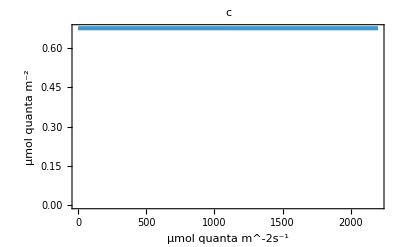
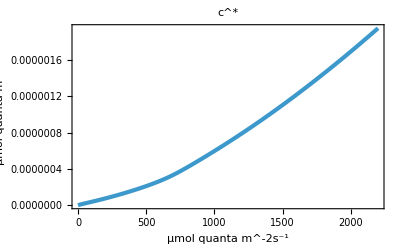
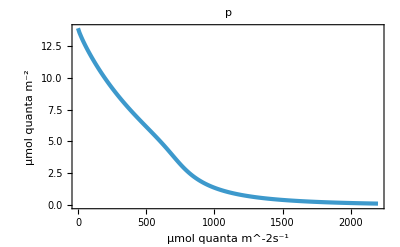
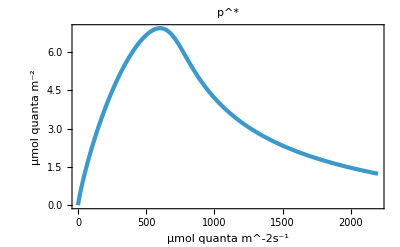
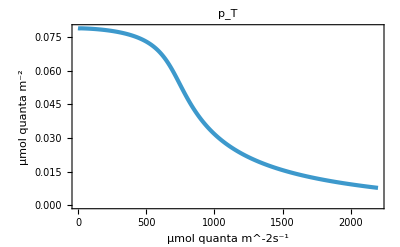
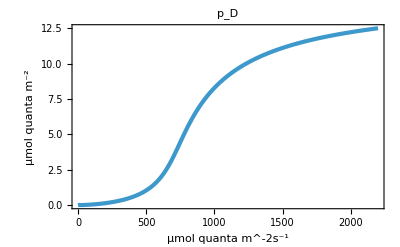
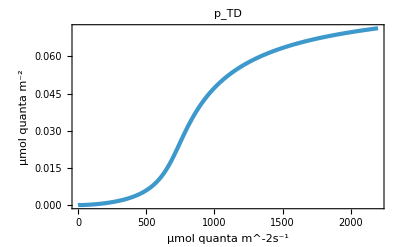
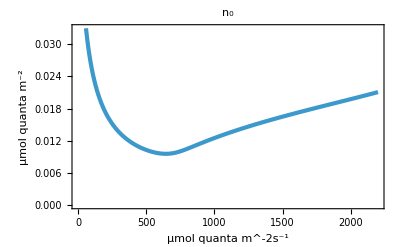

```mathematica
(Export[NotebookDirectory[]<>figureNumberSteadyState1DLong<>"/"<>figureNumberSteadyState1DShort<>"_light_SI"<>".pdf",#];#)&@GridMap[makeOneSimulationSteadyStatePlot[pars[-6],L,Lrange,#,24 3600,{PlotLabel->#/.names}]&,quants]
```

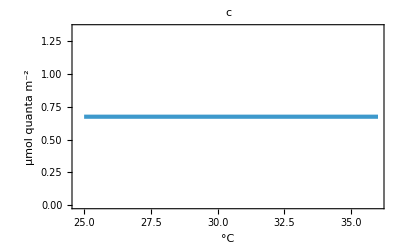
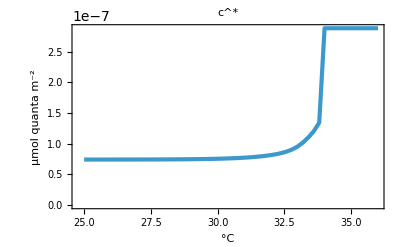
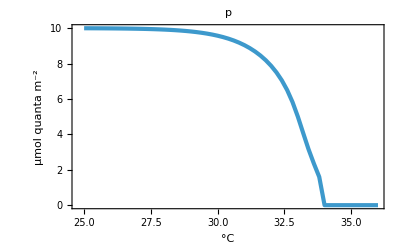
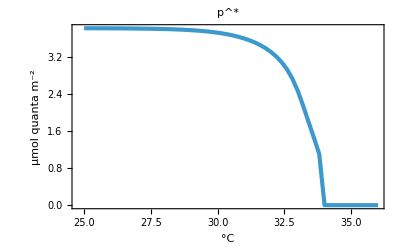
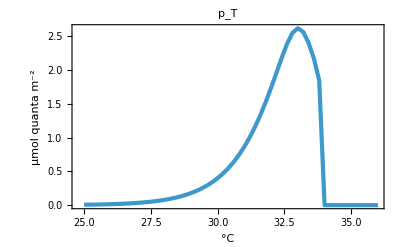
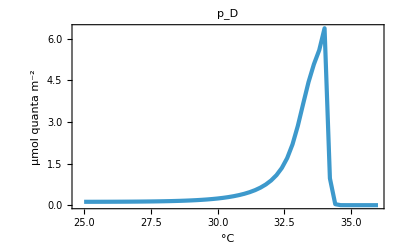
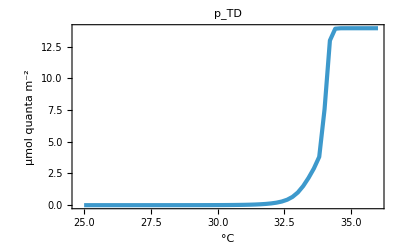
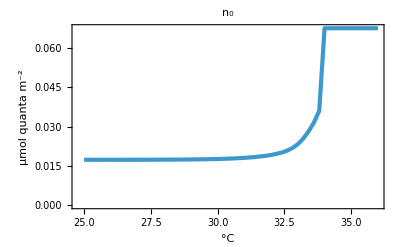

```mathematica
(Export[NotebookDirectory[]<>figureNumberSteadyState1DLong<>"/"<>figureNumberSteadyState1DShort<>"_temperature_SI"<>".pdf",#];#)&@GridMap[makeOneSimulationSteadyStatePlot[pars[-6],w,wRange1D,#, 24 3600,{PlotRange->Full,AxesOrigin->{Automatic,0},PlotLabel->#/.names}]&,quants]
```